# Neural Network Training - YOLO V8

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\PINKY\OneDrive\Documents\College\2024-2025\Fall '24\CHEM 280 - Molecular Modeling\Weed Project

```mathematica
"C:\\Users\\PINKY\\OneDrive\\Documents\\College\\2024-2025\\Fall '24\\CHEM 280 - Molecular Modeling\\Weed Project"
```

C:\Users\PINKY\OneDrive\Documents\College\2024-2025\Fall '24\CHEM 280 - Molecular Modeling\Weed Project

## Data Prep

```mathematica
sowStandard=Thumbnail/@Import["Cropped Annual Sowthistle - Standard","*"];
```

```mathematica
sowDrought=Thumbnail/@Import["Cropped Annual Sowthistle - Drought","*"];
```

```mathematica
sowInjury=Thumbnail/@Import["Cropped Annual Sowthistle - Injury","*"];
```

```mathematica
sowOverwatered=Thumbnail/@Import["Cropped Annual Sowthistle - Overwatered","*"];
```

```mathematica
sowStandardLabels=Thread[sowStandard->"standard"];
```

```mathematica
sowDroughtLabels=Thread[sowDrought->"drought"];
```

```mathematica
sowInjuryLabels=Thread[sowInjury->"injury"];
```

```mathematica
sowOverwateredLabels=Thread[sowOverwatered->"overwatered"];
```

```mathematica
ResourceFunction["TrainTestSplit"]
```

```mathematica
{sSTrain,sSTest}=[sowStandardLabels];
```

```mathematica
{sDTrain,sDTest}=[sowDroughtLabels];
```

```mathematica
{sITrain,sITest}=[sowInjuryLabels];
```

```mathematica
{sOTrain,sOTest}=[sowOverwateredLabels];
```

```mathematica
totalTraining=RandomSample[Join[sSTrain,sDTrain,sITrain,sOTrain]];
```

```mathematica
totalTesting=RandomSample[Join[sSTest,sDTest,sITest,sOTest]];
```

## Network Prep

```mathematica
tempNet=Take[NetModel["YOLO V8 Classify Trained on ImageNet Competition Data"],{1,-3}]
```

NetChain[<23>]

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[4],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"standard","drought","injury","overwatered"}}]]
```

NetChain[<3>]

```mathematica
trainedNet=NetTrain[newNet,totalTraining,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<3>]

```mathematica
ClassifierMeasurements[trainedNet,totalTesting,"Accuracy"]
```

0.727273

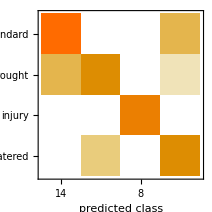
Classifier Measurements
Classifier method | Net
Number of test examples | 44
Accuracy | (73.7.) %
Accuracy baseline | (32.7.) %
Geometric mean of probabilities | 0.479 ± 0.031
Mean cross entropy | 0.737 ± 0.064
Single evaluation time | 25.1 ms/example
Batch evaluation speed | 64.1 examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[trainedNet,totalTesting]
```